```mathematica
SetDirectory[StringDrop[NotebookDirectory[],-4]]
```

H:\2_Programming\physics\5d_flavourful_axion

```mathematica
<<"WarpFlavourAxion`"
```

```mathematica
cubeHelixColor[l_,s_,r_,h_,g_]:=With[
{ψ=2 π (s/3+r l),a=h l^g (1-l^g)/2},
RGBColor[
l^g+a{{-0.14861,1.78277},{-0.29227,-0.90649},{1.97294,0.0}}.{Cos[ψ],Sin[ψ]}
]
]
```

```mathematica
colors=Table[
cubeHelixColor[0.5,s,π/6,1,1],
{s,{0,0.15,0.3,0.5,0.8,1,1.5,1.8,2.0,2.2,2.4,2.6}}
]//Flatten
```

{RGBColor[{0.7236100438261407, 0.3897060587723205, 0.48173308035896434}],RGBColor[{0.7132897054833467, 0.40895632946827126, 0.40662747026197715}],RGBColor[{0.6820910846910813, 0.43711858897442013, 0.3406618139404164}],RGBColor[{0.6135535576997629, 0.4836737789354366, 0.2778762042137195}],RGBColor[{0.4786343604757513, 0.5561096332061026, 0.25731664278722743}],RGBColor[{0.38994351387362236, 0.593967720163116, 0.2961431238547551}],RGBColor[{0.27638995617385936, 0.6102939412276795, 0.5182669196410356}],RGBColor[{0.3179089153089188, 0.5628814110255798, 0.6593381860595837}],RGBColor[{0.38644644230023706, 0.5163262210645634, 0.7221237957862805}],RGBColor[{0.47461841101953034, 0.46694807916242187, 0.7465021832901948}],RGBColor[{0.5671790870580439, 0.42328491464037193, 0.7282581039012023}],RGBColor[{0.6481238886413754, 0.3928864853116728, 0.6705461246879174}]}

#### Load data

```mathematica
quarkData = <<"output/yukawa_quark.m";
Print["Number of Yu Yd 3x3 matrix pairs"]
Dimensions[quarkData]
```

Number of Yu Yd 3x3 matrix pairs

{861,2,3,3}

```mathematica
leptonData = <<"output/yukawa_lepton.m";
Print["Number of Yn Ye 3x3 matrix pairs (normal hierarchy)"]
Dimensions[leptonData[[1]]]
Print["Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)"]
Dimensions[leptonData[[2]]]
```

Number of Yn Ye 3x3 matrix pairs (normal hierarchy)

{4323,2,3,3}

Number of Yn Ye 3x3 matrix pairs (inverted hierarchy)

{3975,2,3,3}

#### Plotting UV case

```mathematica
simulateQuarkDataUV[ptclLabel_,nTrials_,cMmin_,cMmax_,cMstep_,seed_:0.4]:=Module[{yu,yd,myu,myd,output={},temp},
Do[
{yu,yd}=quarkData[[i]];
myu=Minors[yu];myd=Minors[yd];
temp=Table[
{cM,cP/.FindRoot[FermionProfileUVOverlapCM[cP,cM]==QuarkEffMass[yu,yd,myu,myd][ptclLabel],{cP,Norm[cM]+seed}][[1]]//Quiet},{cM,cMmin,cMmax,cMstep}];
AppendTo[output,temp],
{i,nTrials}];
output
]
```

```mathematica
simulateLeptonDataUV[ptclLabel_,nTrials_,cMmin_,cMmax_,cMstep_,seed_:0.4]:=Module[{yu,yd,myu,myd,output={},temp},
Do[
{yu,yd}=leptonData[[1,i]];
myu=Minors[yu];myd=Minors[yd];
temp=Table[
{cM,cP/.FindRoot[FermionProfileUVOverlapCM[cP,cM]==LeptonEffMass[yu,yd,myu,myd][ptclLabel],{cP,Norm[cM]+seed}][[1]]//Quiet},{cM,cMmin,cMmax,cMstep}];
AppendTo[output,temp],
{i,nTrials}];
output
]
```

```mathematica
listableMin[data_,col_:2]:=Module[{
pos=Table[data[[1,i,1]],{i,Dimensions[data][[2]]}]
},
Transpose[{pos, Min/@Table[data[[All,i,2]],{i,Dimensions[data][[2]]}]}]
]
```

```mathematica
listableMax[data_,col_:2]:=Module[{
pos=Table[data[[1,i,1]],{i,Dimensions[data][[2]]}]
},
Transpose[{pos, Max/@Table[data[[All,i,2]],{i,Dimensions[data][[2]]}]}]
]
```

```mathematica
n = 101;
```

```mathematica
UVdataQuark=simulateQuarkDataUV[#,n,0.05,6.05,0.1]&/@{"u","d","s","c","b","t"};
```

```mathematica
UVdataLepton=simulateLeptonDataUV[#,n,-6.05,6.05,0.2]&/@{"e","mu","tau"};
```

```mathematica
SetOptions[ListPlot,{Joined->True,AspectRatio->1,Frame->True,Axes->False,ImageSize->Medium}];
```

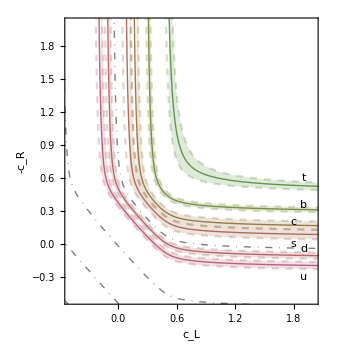

```mathematica
With[
{min=-1/2,max=2},
Show[
ListPlot[{},
PlotRange->{{min,max},{min,max}},
FrameLabel->{"c_L","-c_R"},
GridLines->{{1/2},{1/2}}],

MapThread[ListPlot[{
TurnLeft[Mean[#1]],
TurnLeft[Mean[#1]+StandardDeviation[#1]],
TurnLeft[Mean[#1]-StandardDeviation[#1]]
},
PlotRange->{{min,max},{min,max+5}},
PlotStyle->{
{Thick,#2},
{Dashed,Opacity[0.3],#2},
{Dashed,Opacity[0.3],#2}
},
Filling->{2->{3}}]&,
{UVdataQuark,colors[[{1,2,3,4,5,6}]]}],

(* Generate reference lines *)
ContourPlot[FermionProfileUVOverlap[cL,cR],
{cL,min-0.1,max+0.1},{cR,min-0.1,max+0.1},
ContourStyle->Directive[Opacity[0.5],DotDashed],
ContourShading->None,
Contours->10^Range[-16,-2,4],
ContourLabels->(10^ToString/@Range[-22,-2,4]),
PlotPoints->100
],

(* Generate labels *)
Epilog->MapThread[Inset[#1,{#2,#3}]&,
{{"u","d","s","c","b","t"},
{1.9, 1.9, 1.8,1.8,1.9,1.9},
{-0.3,- 0.05, 0.,0.2,0.35,0.6}}
]
]
]
```

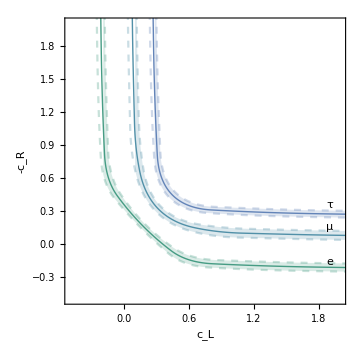

```mathematica
With[{min=-1/2,max=2},Show[ListPlot[{},PlotRange->{{min,max},{min,max}},FrameLabel->{"\!\(\*SubscriptBox[\(c\), \(L\)]\)","-\!\(\*SubscriptBox[\(c\), \(R\)]\)"},GridLines->{{1/2},{1/2}}],MapThread[ListPlot[{TurnLeft[Mean[#1]],TurnLeft[Mean[#1]+StandardDeviation[#1]],TurnLeft[Mean[#1]-StandardDeviation[#1]]},PlotStyle->{{Thick,#2},{Dashed,Opacity[0.3],#2},{Dashed,Opacity[0.3],#2}},Filling->{3->{2}}]&,{UVdataLepton,colors⟦{7,8,9}⟧}],Epilog->MapThread[Inset[#1,{#2,#3}]&,{{"e","μ","τ"},{1.9,1.9,1.9},{-0.17,0.15,0.35}}]]]
```